# NG^4 T_15.Репродуктивный план Холланда

Шклярик Вера
23-май-2023

## Section. Селекционная привлекательность

```mathematica
SetDirectory@NotebookDirectory[]
Get["NG23T15Problem.mx","NG23T15"]
```

C:\Users\asus\Desktop\НСиГА\лаб15

```mathematica
at^2+b t +c
% ==f/.{{t->μ-2σ, f->4}, {t->μ,f->2}, {t->μ+2σ,f->1}}
First@Solve[%,{a,b,c}]
%%%/.%
%//Simplify
```

at^2+c+b t

{at^2+c+b (μ-2 σ)==4,at^2+c+b μ==2,at^2+c+b (μ+2 σ)==1}

First::nofirst: {} has zero length and no first element.

First[{}]

ReplaceAll::reps: {First[{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

at^2+c+b t/.First[{}]

at^2+c+b t/.First[{}]

```mathematica
ClearAll[Fitness];
Fitness[{μ_,σ_}]:=With[{$ =  (#^2+ μ^2+ 6μ σ + 16 σ^2 - 2#(μ +3σ))/(8. σ^2)//Expand}, $&];
```

```mathematica
Fitness@{11,3}
```

6.43056-0.555556 #1+0.0138889 #1^2&

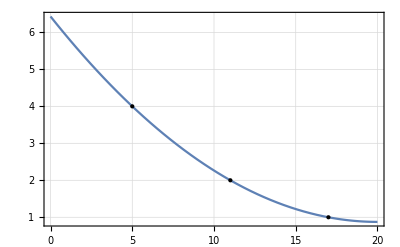

```mathematica
Plot[%@t, {t,0,20},Frame->True, GridLines->Automatic, Epilog->{PointSize@Large, Point@{{5,4},{11,2},{17,1}}}]
```

## Section. Инициализация популяции

```mathematica
ClearAll[Population];
Population::"usage"="Популяция, реализующая генетический алгоритм оптимизации";
SetAttributes[Population,{HoldAllComplete,ReadProtected}];
(************************************)
(***Конструктор популяции особей***)
Population["Init",OptionsPattern[]]:=Association["best"->{∞,{}},(*фенотип лучших за все поколения особей*)"genotype"->(*генотип текущей популяции*)StringJoin@@@RandomChoice[{"0","1"},{OptionValue@"size"+OptionValue@"surplus",OptionValue@"genomLen"}],"trouble"->{},(*проблемность особей текущей популяции*)
"weight"->{},(*селекционная привлекательность особей текущей популяции*)
"progeny"->{},(*генотип популяции следующего поколения*)
"param"->Association[(***вспомогательные параметры:***)
"size"->OptionValue@"size",
"surplus"->OptionValue@"size"+OptionValue@"surplus",
"genomLen"->OptionValue@"genomLen",
"eliteCount"->OptionValue@"eliteCount",
"pc"->OptionValue@"pc",
"pm"->OptionValue@"pm",
"pi"->OptionValue@"pi",
"ps"->OptionValue@"ps"]];
(****************************************)
(***значения параметров по умолчанию***)
Options[Population]={
"size"->10,(*размер популяции*)
"surplus"->3,(*максимальный прирост популяции в следующем поколении*)
"genomLen"->39,(*длина генома (хромосомы)*)
"eliteCount"->2,(*количество элитных особей*)
"pc"->0.9,(*вероятность скрещивания*)
"pm"->0.1,(*вероятность мутации*)
"pi"->0.01,(*вероятность инверсии*)
"ps"->0.8,(*вероятность выживания особи*)
ImageSize->{UpTo@200,UpTo@350}};
(***************)
(**Декоратор**)
Population[P_Symbol,"Show",OptionsPattern[]]:=Image[ToExpression@Map[Characters, P@"genotype"],ImageSize->OptionValue@ImageSize];
```

```mathematica
X = Population["Init", "size"->3, "surplus"->1]
```

<|best→{∞,{}},genotype→{100110110110001111000000010100001111101,111101111110000111101000000001111011110,100000111011110001000100110000010100101,110101010011001000010000000010011101010},trouble→{},weight→{},progeny→{},param→<|size→3,surplus→4,genomLen→39,eliteCount→2,pc→0.9,pm→0.1,pi→0.01,ps→0.8|>|>

```mathematica
X = Population["Init"]
Population[X, "Show"]
```

<|best→{∞,{}},genotype→{111110111010010101000011011110101001111,010101011110001110001011000110111110110,001101010101011100100000011100011100000,111111010101000010001001111111100110110,000101111111011101011111010000110000011,010111101001100000000110101000100001101,100010110111111110111001111111010010110,000111001111010101000010101100000110000,101010011010001110001100010010001111011,110101011001001010111011010111100100110,111100111001110001111001011111100100001,000111111001011010001100111011010000000,010000111101010001101010001011011101001},trouble→{},weight→{},progeny→{},param→<|size→10,surplus→13,genomLen→39,eliteCount→2,pc→0.9,pm→0.1,pi→0.01,ps→0.8|>|>

-Graphics-

## Section. Репродуктивный план

### Section.Subsection. Фенотип поколения

```mathematica
ClearAll[AnalogToDigital,DigitalToAnalog];
AnalogToDigital[{from_,to_},bits_Integer]:= With[{$ = Min[2^bits-1,N@Floor[(#-from)/(to - from)2^bits]]},$&];
DigitalToAnalog[{from_,to_},bits_Integer]:= With[{$ = from + (#+0.5) 2^-bits(to - from)//Expand//N}, $&];
```

```mathematica
ClearAll[GrayTable,ToGray,FromGray];
GrayTable= Nest[Join["0"<>#&/@#,"1"<>#&/@Reverse@#]&,{"0","1"},9];
ToGray[n_Integer,len_Integer:10]:= StringPadLeft[GrayTable[[n+1]],len];
FromGray[g_String]:=Position[GrayTable,StringPadLeft[g,10,"0"]][[1,1]] -1;
```

```mathematica
ClearAll[GenotypeToPhenotype,PhenotypeToGenotype];
GenotypeToPhenotype[chromosome_String] := MapThread[
Apply[DigitalToAnalog, #1]@FromGray@StringTake[chromosome, #2]&,{
{{{0,100},10},{{0,100},10},{{0,10},10}, {{0,359.99},9}},
{{1,10},{11,20},{21,30},{31,39}}}];
PhenotypeToGenotype[{x_,y_,F_,α_}]:=StringJoin[
ToGray[AnalogToDigital[{0,100},10]@x,10],
ToGray[AnalogToDigital[{0,100},10]@y,10],
ToGray[AnalogToDigital[{0,10},10]@F,10],
ToGray[AnalogToDigital[{0,359.99},9]@α,9]
] ;
```

```mathematica
CreatePalette[Pane[Style[Dynamic@X, Small],400]]
```

```mathematica
GenotypeToPhenotype/@X@"genotype";
X@"trouble" = Troubles/@%
Position[%,Min@%]
X@"best"={Extract[%%,%],Extract[%%%,%]}
```

{10.1889,461.559,3.1215,1243.86,317.545,19.7734,577.03,3.70025,36.234,749.529,847.802,146.573,29.7424}

{{3}}

{{3.1215},{{14.9902,40.9668,0.229492,134.645}}}

```mathematica
X = Population["Init"]
Population[X, "Show"]
```

<|best→{∞,{}},genotype→{000111111100100111011010101101010110001,110100011000011111101111110101101010101,010100111101010010010111110101010100011,100010110110000111011111000111101001000,010001101111101101000010010100011001010,110111111111100001110011100010010100110,011110001000111110001111101111000000100,010111011100011100011111111100011110110,010001101010110110101011110011101111110,101011110010000000110001001010000011011,000100011001001100010100101110100100010,001000110101010001011000100001110100100,001111011011100010000011101011000001110},trouble→{},weight→{},progeny→{},param→<|size→10,surplus→13,genomLen→39,eliteCount→2,pc→0.9,pm→0.1,pi→0.01,ps→0.8|>|>

-Graphics-

```mathematica
Population[P_Symbol,"Phenotype"] := Block[
{T,Ph = GenotypeToPhenotype/@P@"genotype"},
T = P@"trouble" = Troubles/@Ph;
P@"best" = {Extract[T, First@#], Extract[Ph, #]}&@Position[T,Min@T]];
```

```mathematica
Population[X,"Phenotype"]
```

{2.44381,{{16.0645,73.4863,1.74316,8.08571}}}

### Section.Subsection. Элитаризм

```mathematica
X = Population["Init"];
Population[X, "Show"]
Population[X,"Phenotype"]
```

-Graphics-

{3.51689,{{22.2168,6.5918,0.0341797,296.359}}}

```mathematica
X[["param", "eliteCount"]]
X["param", "eliteCount"]
Ordering[X@"trouble",%]
X[["genotype",%]]
```

2

2

{9,1}

{001001001000011000100000000010101110111,011001011110111110000000111111000111010}

```mathematica
Population[P_Symbol,"Elite"]:=Set[P@"progeny", P[["genotype",Ordering[P@"trouble",P["param", "eliteCount"]]]]];
```

```mathematica
X = Population["Init"];
Population[X, "Show"];
Population[X,"Phenotype"];
Population[X, "Elite"];
```

### Section.Subsection. Элиминация

```mathematica
X[["param","size"]]-X[["param","surplus"]]
List/@Ordering[X@"trouble",%]
Delete[X@"trouble", %]
```

-3

{{9},{2},{4}}

{9.39682,19.6309,7.97074,153.178,22.5117,4.87954,6.34265,8.25373,3.48023,101.233}

```mathematica
Population[P_Symbol,"Elimination"]:=Block[
{pos = List/@Ordering[P@"trouble",P[["param","size"]]-P[["param","surplus"]]]},
P@"trouble" = Delete[P@"trouble", pos];
P@"genotype" = Delete[P@"genotype", pos];
];
```

```mathematica
X = Population["Init"];
Population[X, "Show"];
Population[X,"Phenotype"];
Population[X, "Elite"];
Population[X,"Elimination"]
```

### Section.Subsection. Селекционная привлекательность

```mathematica
X@"trouble"
Through@{Mean, StandardDeviation}@%
Fitness@%
%/@%%%
```

{86.806,4.9815,391.061,10.7461,2.74556,6.83007,151.026,37.1004,7.7661,7.55402}

{70.6617,122.488}

2.47426-0.00730047 #1+8.33147×10^-6 #1^2&

{1.90332,2.4381,0.893456,2.39677,2.45428,2.42479,1.56173,2.21488,2.41807,2.41959}

```mathematica
Population[P_Symbol,"Fitness"]:= Set[P@"weight",Map[Fitness@Through@{Mean, StandardDeviation}@#,#]&@P@"trouble"];
```

```mathematica
X = Population["Init"];
Population[X, "Show"];
Population[X,"Phenotype"];
Population[X, "Elite"];
Population[X,"Elimination"]
```

```mathematica
Population[X,"Fitness"]
```

{1.34769,1.53097,2.1753,2.56253,0.969659,2.73659,2.21436,2.09358,2.73898,2.75534}

### Section.Subsection. Скрещивание

```mathematica
X = Population["Init"];
Population[X, "Show"];
Population[X,"Phenotype"];
Population[X, "Elite"];
Population[X,"Elimination"]
Population[X,"Fitness"]
```

{2.49962,2.59624,1.36905,2.2262,0.939462,2.69232,2.00458,1.67566,2.43833,2.68353}

```mathematica
RandomSample[X@"weight"->Range@X["param","size"],2]
Ordering[X[["weight",%]]]
```

{8,1}

{1,2}

```mathematica
Population[P_Symbol,"Crossover"]@{parent1_,parent2_}:=With[{$ = RandomInteger[{2,P[["param","genomLen"]]-1}]},If[RandomChoice[{False,True}], StringTake[parent1, $]<>StringDrop[parent2,$], StringTake[parent2, $]<>StringDrop[parent1,$]]]
```

```mathematica
{$1,$2} = RandomSample[X@"weight"->X@"genotype",2]
RandomInteger[{2,X[["param","genomLen"]]-1}]
If[RandomChoice[{False,True}], StringTake[$1, %]<>StringDrop[$2,%], StringTake[$2, %]<>StringDrop[$1,% ]]
```

{010000010100010000110101110111101000101,101010010111001111000101000111111010111}

14

010000010100011111000101000111111010111

```mathematica
X = Population["Init"];
Population[X, "Show"];
Population[X,"Phenotype"];
Population[X, "Elite"];
Population[X,"Elimination"]
Population[X,"Fitness"];
{$1,$2} = RandomSample[X@"weight"->X@"genotype",2]
Population[X,"Crossover"]@%
```

{111010010100100111111101100001111001111,011111001010010001100011100001000111010}

111010010100100001100011100001000111010

### Section.Subsection. Мутация

```mathematica
Population[P_Symbol,"Mutation"]@{individual_}:=
With[{$= RandomInteger[{2,X[["param","genomLen"]]-1}]},StringReplacePart[individual,If[StringPart[individual,$]=="0","1","0"],{$,$} ]]
```

```mathematica
X = Population["Init"];
Population[X, "Show"];
Population[X,"Phenotype"];
Population[X, "Elite"];
Population[X,"Elimination"]
Population[X,"Fitness"];
$1= RandomSample[X@"weight"->X@"genotype",1]
Population[X,"Mutation"]@%
```

{111001001111010010010100111000011111111}

111001001111010010010100111100011111111

### Section.Subsection. Инверсия

```mathematica
Population[P_Symbol,"Inversion"]@{individual_}:=With[{$= RandomInteger[{2,X[["param","genomLen"]]-1}]},StringRotateLeft[individual, $]]
```

```mathematica
X = Population["Init"];
Population[X, "Show"];
Population[X,"Phenotype"];
Population[X, "Elite"];
Population[X,"Elimination"]
Population[X,"Fitness"];
$1= RandomSample[X@"weight"->X@"genotype",1]
Population[X, "Inversion"]@%
```

{011001111101011010010101011110000010111}

011010010101011110000010111011001111101

### Section.Subsection. Выживание

```mathematica
Population[P_Symbol,"Adult"]@{id_Integer,individual_}:={P@"weight" = Delete[P@"weight", id];
P@"genotype" = Delete[P@"genotype", id];
Set[P@"progeny", Append[P@"progeny",individual]];}
```

```mathematica
X = Population["Init"];
Population[X, "Show"];
Population[X,"Phenotype"];
Population[X, "Elite"];
Population[X,"Elimination"]
Population[X,"Fitness"];
```

```mathematica
$1= RandomSample[X@"weight"->X@"genotype",1]
Population[X, "Adult"]@{2, %};
```

{010101000011101010000111011001110011100}

### Section.Subsection. Генерация нового поколения

## Section. Оптимизация генетическим алгоритмом